# M1: Equations and Matrices

Numerical Linear Algebra underlies almost every technical computation: NLA encodes, solves amd analyzes equations after linearization

## Preamble

## Fitting Data with Polynomials

Suppose I have a bunch of points from a function and I want to run a polynomial p through the points!

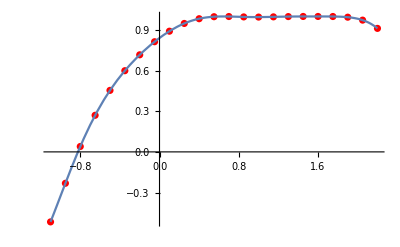

```mathematica
f[x_]:=Sin[x+ Cos[x Sin[x]]]
{a,b}={-1.1,2.2};m=23;
xs=Table[x,{x,a,b,(b-a)/(m-1)}];
fs=Map[f,xs];
Data=Transpose[{xs,fs}];
Show[ListPlot[Data,PlotStyle->Red],Plot[f[x],{x,a,b}]]
```

The polynomial is simply a sum p[x]=c_0+c_1 x+c_2 x^2+… We have m points we should be able to choose m constants to go through the m points. The m equations are 
	c_0 | + | c_1 x_1^1 | + | c_2 x_1^2 | + | … | + | c_(m-1)x_1^(m-1) | = | f(x_1)
c_0 | + | c_1 x_2^1 | + | c_2 x_2^2 | + | … | + | c_(m-1)x_2^(m-1) | = | f(x_2)
  |   |   |   |   |   |   |   |   | ⋮ |  
c_0 | + | c_1 x_m^1 | + | c_2 x_m^2 | + | … | + | c_(m-1)x_m^(m-1) | = | f(x_m)
This is 
	A.c=f
where c={c_0,c_1,…,c_(m-1)}, f={f(x_1),f(x_2),…,f(x_m)}, and A_(i,j)=(x_i)^(j-1).  Lets build them and solve.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{1.,-1.1,1.21,-1.331,1.4641,-1.61051,1.77156,-1.94872,2.14359,-2.35795,«13»},«9»,«13»} may contain significant numerical errors.

0.841471+0.540302 x-0.420741 x^2-0.0900499 x^3-0.234909 x^4+0.424952 x^5+0.222032 x^6-0.205859 x^7-0.143577 x^8-0.0844214 x^9+0.103765 x^10+0.154077 x^11-0.0609431 x^12-0.129994 x^13+0.0688137 x^14+0.0531943 x^15-0.0583393 x^16+0.00987264 x^17+0.0129491 x^18-0.00994152 x^19+0.00330419 x^20-0.000562076 x^21+0.0000398195 x^22

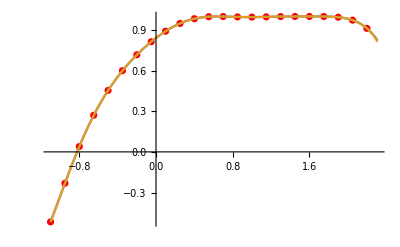

```mathematica
Clear[p]
A=Table[x^(j-1),{x,xs},{j,m}]; 
as=LinearSolve[A,fs];
p[x_]=Sum[as[[j]] x^(j-1),{j,1,m}]
Show[ListPlot[Data,PlotStyle->Red],Plot[{f[x],p[x]},{x,a,b+0.11}],
PlotRange->All]
```

Q1: Is using m large a good idea?
Q2: How was this computed?
Q3: Does software/algorithm make any difference? 
Q4: What does the warning mean?

## Basics

## Multiplying Matrices and Vectors

Random matrices are easy in Mathematica a dot means matrix-vector and matrix-matrix multiplication

```mathematica
{m,n}={6,5};
A=RandomReal[{-1,1},{m,n}];
b=RandomReal[{-1,1},n];
A.b
```

{0.64571,-0.753365,-0.389241,0.176365,0.589214,0.299523}

You get a warning if dimensions do not match!

```mathematica
{m,n}={6,5};
A=RandomReal[{-1,1},{m,n}];
b=RandomReal[{-1,1},m];
A.b
```

Dot::dotsh: Tensors {{-0.497646,-0.12317,-0.273019,-0.47798,0.722175},«4»,{0.97559,0.150869,0.554334,-0.718004,-0.143689}} and {-0.142328,0.491866,-0.87372,0.832738,0.984187,-0.0862579} have incompatible shapes.

{{-0.497646,-0.12317,-0.273019,-0.47798,0.722175},{0.0119647,0.970378,-0.878201,-0.126754,-0.455364},{0.943591,0.0483172,0.692733,0.824927,-0.222679},{-0.811524,0.195105,-0.589158,-0.281803,0.0445548},{0.126624,-0.0617333,0.74385,0.591444,0.824739},{0.97559,0.150869,0.554334,-0.718004,-0.143689}}.{-0.142328,0.491866,-0.87372,0.832738,0.984187,-0.0862579}

It works the same for matrix-matrix multiplication

```mathematica
{m,n,r}={6,5,12};
A=RandomReal[{-1,1},{m,n}];
B=RandomReal[{-1,1},{n,r}];
Dimensions[A.B]
```

{6,12}

## Multiplying Matrices from scratch: Efficiency!

If C=A.B the C_(i,j)=∑_k A_(i,k)B_(k,j). Defining this yourself is slower (in every way you can imagine) than the built in command!

```mathematica
{m,r,n}={6,5,12};
A=RandomReal[{-1,1},{m,r}];
B=RandomReal[{-1,1},{r,n}];
CBuiltIn=A.B;
CFormula1=Table[
Sum[A⟦i,k⟧B⟦k,j⟧,{k,r}],
{i,m},{j,n}];
Norm[CBuiltIn-CFormula1]
```

5.16129×10^-16

If C=A.B then C=(c_1 | | | c_2 | | | …) where c_j=A.b_j you can implement this.  It will also be slower than the built in matrix multiplication.

```mathematica
{m,n,r}={6,5,12};
A=RandomReal[{-1,1},{m,r}];
B=RandomReal[{-1,1},{r,n}];
CBuiltIn=A.B;
CFormula2=Table[
A.B⟦All,j⟧,
{j,n}]ᵀ;
Norm[CBuiltIn-CFormula2]
```

4.36613×10^-16

We can (and should) race and compare all our versions!

```mathematica
{m,r,n}={12,23,45};
A=RandomReal[{-1,1},{m,r}];
B=RandomReal[{-1,1},{r,n}];
Timing[CBuiltIn=A.B;]
Timing[CFormula1=Table[
Sum[A⟦i,k⟧B⟦k,j⟧,{k,r}],
{i,m},{j,n}];]
Timing[CFormula2=Table[
A.B⟦All,j⟧,
{j,n}]ᵀ;]
```

{0.,Null}

{0.015625,Null}

{0.,Null}

## Block Matrices and Blocks of Matrices

A block matrix 
	A=(A_11 | A_12
A_21 | A_22
A_31 | A_33)
simply slams matrices (of matching dimensions) together.

```mathematica
{m,n}={2,3};
{{A11,A12},
{A21,A22},
{A31,A32}}=RandomReal[{-1,1},{3,2,m,n}];
A=ArrayFlatten[{{A11,A12},{A21,A22},{A31,A32}}];
Dimensions[A];
Map[MatrixForm,{A,A31}]
```

{(0.349863 | -0.247999 | -0.00368938 | 0.682078 | -0.741388 | 0.457394
-0.273477 | 0.812848 | -0.679496 | -0.252186 | -0.521447 | -0.626528
0.770709 | 0.533702 | 0.884015 | -0.985607 | 0.155655 | -0.789783
-0.343634 | -0.390965 | 0.367658 | 0.785337 | 0.347738 | 0.1065
0.0478359 | -0.930422 | -0.784937 | 0.759485 | 0.202348 | -0.16522
-0.747446 | 0.197068 | -0.750136 | -0.994013 | 0.594556 | -0.853737),(0.0478359 | -0.930422 | -0.784937
-0.747446 | 0.197068 | -0.750136)}

You can grab a chunk of a matrix using the range notation

```mathematica
Map[MatrixForm,{A[[1;;m,1;;n]],A11}]
```

{(0.349863 | -0.247999 | -0.00368938
-0.273477 | 0.812848 | -0.679496),(0.349863 | -0.247999 | -0.00368938
-0.273477 | 0.812848 | -0.679496)}

## Inverse Matrices and Linear Solves

Almost all random square matrices A have an inverse A^-1 satisfying A^-1.A=Id

```mathematica
m=23;
A=RandomReal[{-1,1},{m,m}];
AInv=Inverse[A];
Norm[A.AInv-IdentityMatrix[m]]
```

3.3134×10^-13

Most of the time you do not want the inverse! You just want to solve the system A.x=b. It is almost always better (faster and more accurate) to solve the system than compute and apply the inverse.

```mathematica
m=2345;
A=RandomReal[{-1,1},{m,m}]; x=RandomReal[{-1,1},m];
b=A.x;
Timing[AInv=Inverse[A]; xSlow=AInv.b;]
Timing[xFast=LinearSolve[A,b];]
Map[Norm,{xSlow-x,xFast-x}]
```

{0.265625,Null}

{0.140625,Null}

{1.5887×10^-10,1.36627×10^-11}

## Definitions and Theorems

The square matrix V_(i,j)=(x_i)^(j-1) defined by a list x_1,…,x_m is the Vandermonde matrix.

The range (or column space) of a matrix A is the span of columns of A and column rank is its dimension.

The row space of a matrix A is the span of rows of A and row rank is its dimension.

The null space of a matrix A is the set of solutions of A x=0.

A diagonal matrix has zero entries everywhere except on the diagonal.

The m×m identity matrix I_m is the diagonal matrix with 1s on the diagonal.

The inverse A^-1 of an m×m matrix A satisfies A A^-1= A^-1 A=I_m.

Any linear map from L:ℝ^n→ℝ^m is represented A=(L(e_1) | | | L(e_2) | | | … | | | L(e_n))∈ℝ^(m×n).

Theorem 1.3
For A∈ℂ^(m×m) the following are all equivalent: A is invertible; rank(A)=m; range(A)=ℂ^m; null(A)={0}; 0 is not an eigenvalue of A; 0 is not a singular value of A; and det(A)≠0.

## Adjoint and Inner Product

The inner product of two vectors x,y∈ℂ^m is the scalar <x,y>=∑_(i=1)^m OverBar[x_i]y_i

The Euclidean norm of a vector x∈ℂ^m is the scalar ||x||=√(<x,x>)=√(∑_(i=1)^m |x_i|^2)

The angle α between two vectors x,y∈ℝ^m satisfies cos(α)=(<x,y>)/(||x|| ||y||)

The transpose Aᵀ∈ℂ^(n×m) of  A∈ℂ^(m×n) satisfies (Aᵀ)_(i,j)=A_(j,i)

The adjoint of A^*=OverBar[Aᵀ]∈ℂ^(n×m) is the complex conjugate of Aᵀ for A∈ℂ^(m×n).

These definitions make <x,A y> =<A^*x,y>

```mathematica
IP[x_,y_]:=Sum[Conjugate[x⟦i⟧] y⟦i⟧,{i,Length[x]}]
{m,n}={3,4};
A=RandomComplex[{-1-I,1+I},{m,n}];
x=RandomComplex[{-1-I,1+I},m];
y=RandomComplex[{-1-I,1+I},n];
AStar=ConjugateTranspose[A];
{IP[x,A.y],IP[AStar.x,y]}
```

{-1.03755+0.250494 ⅈ,-1.03755+0.250494 ⅈ}

## Orthogonality

Vectors x,y∈ℂ^m are orthogonal if <x,y> =0.

A set of n vectors {x_1,x_2,…,x_n}⊂ℂ^m are orthogonal if <x_i,x_j> =0 for i!=j.

A matrix Q∈ℂ^(m×n) is unitary if Q^*Q=I_n:  Unitary matrix columns q_i are orthogonal with ||q_i||=1.

A matrix Q∈ℝ^(m×n) is orthogonal if QᵀQ=I_n: Orthogonal matrix columns q_i are orthogonal with ||q_i||=1.

Orthogonality gives a simple procedure to split a vector v∈ℂ^m into a piece in the span of the columns of a unitary matrix Q∈ℂ^(m×n) and a residual r∈ℂ^m that is orthogonal to all n columns Q=(q_1 | | | q_2 | | | … | | | q_n).  The recipe is
	r=v-<q_1,v>q_1-<q_2,v>q_2-…-<q_n,v>q_n=v-Q Qᵀ v=(I-QQᵀ)v 
Alternatively we can write
	v=r+∑_(i=1)^n<q_i,v> q_i
and think of the inner products <q_i,v> as a simple recipe for the coefficient of v in each orthogonal direction q_i.

```mathematica
{m,n}={12,4};
Q=Orthogonalize[RandomReal[{-1,1},{n,m}]]ᵀ;
v=RandomReal[{-1,1},m];
r=v-Q.Qᵀ.v
j=1;
r.Q⟦All,j⟧
```

{-0.288071,0.663366,-0.31064,0.560183,-0.312672,-0.178724,0.587947,-0.685884,0.255519,0.432617,0.359529,-0.46472}

-4.16334×10^-17

## Vector Norms

The Euclidean norm ||x(||)_2=√(∑_(i=1)^m |x_i|^2) is the default norm for x∈ℂ^n. However, there are other functions x∈ℂ^m→d(x)∈ℝ which measure distance in the sense that d(x)≥0 for x!=0; d(x+y)≥d(x)+d(y); and d(α x)=|α| d(x).  The most important of these are the p-norms for 1≤p<∞
	||x(||)_p=(∑_(i=1)^m |x_i|^p)^(1/p)
and the limit as p→∞
	||x(||)_∞=max_(1≤i≤m) |x_i|
Every piece of software has a norm function. The default will be the Euclidean two norm.

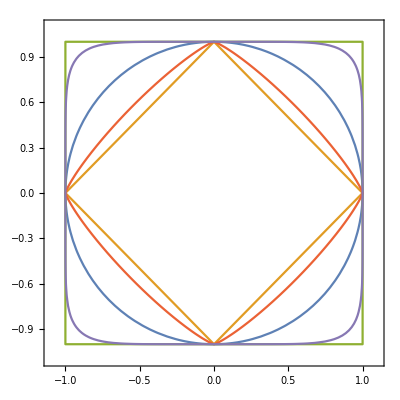

```mathematica
ContourPlot[{
Norm[{x1,x2}]==1,
Norm[{x1,x2},1]==1,
Norm[{x1,x2},∞]==1,
Norm[{x1,x2},1.2]==1,
Norm[{x1,x2},7.2]==1
},{x1,-1.1,1.1},{x2,-1.1,1.1},
Exclusions->None]
```

Rotational invariance is useful.  The Euclidean norm p=2 is the only rotationally invariant vector p-norm. The equivalent 3D pictures are pretty.

```mathematica
ContourPlot3D[{
Norm[{x1,x2,x3}]==1,
Norm[{x1,x2,x3},1]==1,
Norm[{x1,x2,x3},∞]==1,
Norm[{x1,x2,x3},1.2]==1
},{x1,0,1.1},{x2,0,1.1},{x3,0,1.1}]
```

There are other possible distance functions.  For instance, here is a family of exotic vector norms in 3D.

```mathematica
DropSmallNorm[x_,p_]:=Norm[Sort[Abs[x]]⟦2;;-1⟧,p] 
ContourPlot3D[{
DropSmallNorm[{x1,x2,x3},2]==1,
DropSmallNorm[{x1,x2,x3},1]==1
},{x1,0,1.1},{x2,0,1.1},{x3,0,1.1}]
```

## Matrix Norms

Every piece of software computes matrix norms.  There are a lot of possibilities. There is no standard default!

Any function A∈ℂ^(m×n)→d(A)∈ℝ which satisfies d(A)≥0 for A!=0; d(A+B)≥d(A)+d(B); and d(α A)=|α| d(A) is a suitable distance function or norm for matrices.

### Frobenius Norm

The Frobenius norm of A∈ℂ^(m×n) is simply
	||A(||)_F=(∑_(i=1)^m ∑_(j=1)^n|a_(i,j)|^2)^(1/2)
It is unitarily invariant.

### Induced Norms

A matrix norm d(A) is orthogonally invariant if 
	d(Q_1 A Q_2)=d(A) 
for square, conforming, orthogonal matrices Q_1 and Q_2.

The matrix norm for A∈ℂ^(m×n) induced by a vector norm ||x(||)_(n) on the input space ℂ^n and a vector norm ||y(||)_(m) on the output space ℂ^m is
	||A(||)_(m,n)=max_(x∈ℂ^n
x!=0) (||A x(||)_(m))/(||x(||)_(n))=max_(||x(||)_(n)=1) ||A x(||)_(m) 
The most important of these are those induced by the 1,2,∞ vector p norms. Not surprisingly, only the norm induced by the Euclidean (p=2) norm for the input and output spaces is orthogonally invariant.

### SVD based Norms

The Singular Value Decomposition (SVD) of an m×n matrix is A=U Σ Vᵀ where U and V are unitary and Σ is a diagonal m×n matrix with non-increasing, positive diagonal entries.    The singular values of A are the non-diagonal entries of Σ.  Any vector norm of the vector if singular values is a unitarily invariant matrix norm!

The Schatten p-norm of A is just the p-norm of the vector of singular values.

The spectral or operator norm of A is the ∞ norm of the singular values.  So
	||A(||)_op=σ_1
where σ_1 is the largest singular value.

The nuclear norm of A is the 1 norm of the singular values.  So
	||A(||)_*=σ_1+σ_2+…+σ_r=∑_(i=1)^r σ_i
since the r=min(m,n) singular values are positive.

The Ky-Fan k-norm of A just keeps the largest k-singular values (with k≤min(m,n)) in the nuclear norm 
	||A(||)_(KF(k))=∑_(i=1)^k σ_i

The Ky-Fan-Schatten p-k-norm
	(∑_(i=1)^k σ_i^p)^(1/p)
does not have a standard notation.

It turns out that the 2 norm of the singular values is just the Frobenius norm that we met before
	||A(||)_F=(∑_(i=1)^r σ_i^2)^(1/2)

```mathematica
{m,n}={3,4};
RandomReal[{-1,1},{m,n}];
σs=SingularValueList[A];
{Norm[A,"Frobenius"],Norm[σs]}
```

{2.75593,2.75593}

### More on Induced Norms

We are going to get some practice with understanding induced norms.

```mathematica
r[θ,2]
```

{Abs[Cos[θ]] Sign[Cos[θ]],Abs[Sin[θ]] Sign[Sin[θ]]}

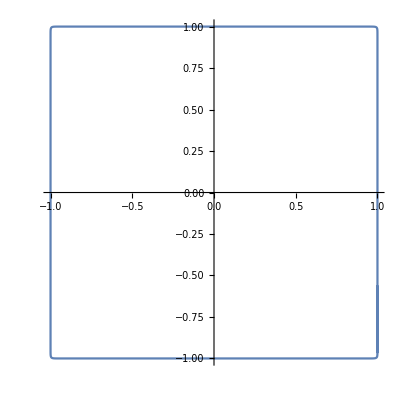

```mathematica
ParametricPlot[r[θ,124],{θ,-π/24, 2π},Exclusions->None]
```

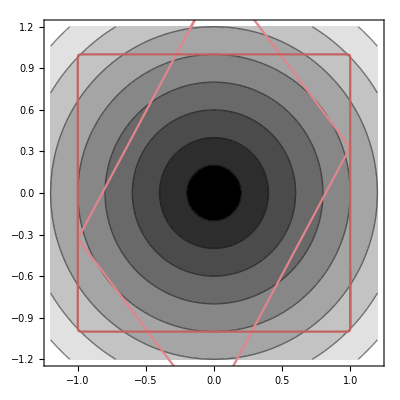

```mathematica
r[θ_,p_]:={Sign[Cos[θ]] Abs[Cos[θ]]^(2/p),Sign[Sin[θ]]*Abs[Sin[θ]]^(2/p)}
A=RandomReal[{-1,1},{2,2}];
{pIn,pOut}={123,2};
Show[
ContourPlot[ Norm[{x1,x2},pOut],{x1,-1.2,1.2},{x2,-1.2,1.2},
ColorFunction->GrayLevel],
ParametricPlot[{A.r[θ,pIn],r[θ,pIn]},{θ,-π/24, 2π},
ColorFunction:>Function[{x1,x2,θ},ColorData["TemperatureMap"][Norm[{x1,x2},pOut]]],
ColorFunctionScaling->True,
Exclusions->None]
]
```

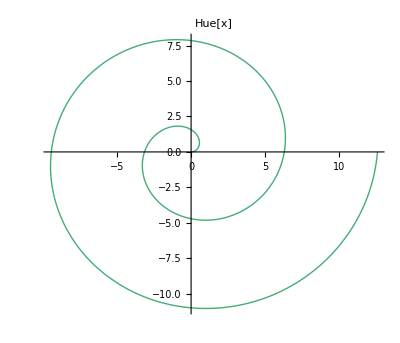
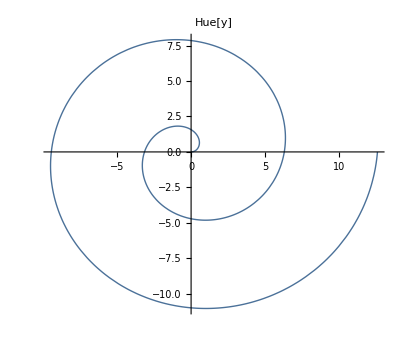
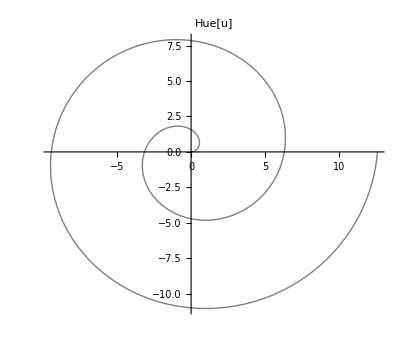
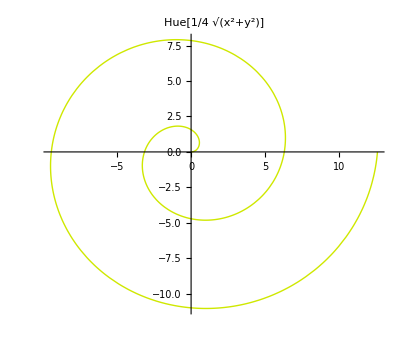

```mathematica
Table[ParametricPlot[{u Cos[u],u Sin[u]},{u,0,4 Pi},ColorFunction->Function[{x,y,u},i],ColorFunctionScaling->True,PlotLabel->i,PlotStyle->Thick],{i,{Hue[x],Hue[y],Hue[u],Hue[(√(x^2+y^2))/4]}}]
```

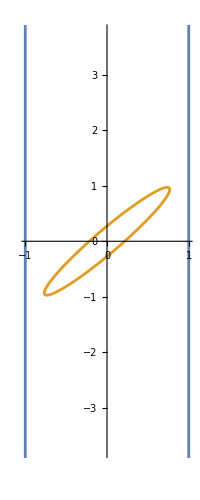

```mathematica
m=2;
p1[θ_]:={Cos[θ],Sin[θ]}/Abs[Cos[θ]]
A=RandomReal[{-1,1},{m,m}];
ParametricPlot[{p1[θ],A.p[θ]},{θ,0, 2π}]
```

```mathematica
We
```

The Singular Value Decomposition (SVD) of an m×n matrix is A=U Σ Vᵀ where U and V are unitary and Σ is a diagonal m×n matrix with non-increasing, positive diagonal entries.    The singular values of A are the non-diagonal entries of Σ.  Any vector norm of the vector if singular values is a unitarily invariant matrix norm!